Select the parameter (.prm) file of the desired chromatogram. It is assumed that the chromatography files are in the same directory as the parameter file.

```mathematica
SystemDialogInput["FileOpen" , {"C:/Users/fskdm/Dropbox", {"Parameter Files"->{"*.prm"}}}]
```

```mathematica
pfile ="C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_20_PhD_Last_Project\\2019_12_23_PAH_FAMEs\\Chromatograms\\RawData\\2020_01_20-183636.dat.prm"
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_01_20-183636.dat.prm

Extract the data directory:

```mathematica
filedir = FileNameJoin[ FileNameSplit[pfile][[1;;-2]]]
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData

Import the parameters:

```mathematica
params = Import[pfile, "Lines"]
```

{GC column description:	Rxi-5Sil MS 0.250 mm x 1 m,SFC flow rate:	0.800,SFC temperature:	22.000,GC flow rate: 	99.000,Experiment title: 	Diesel PAH,Sample name: 	Swedish diesel,Analysis type: 	Standard,Concentration: 	9999.000,Operator name: 	DM,Detector sensitivity: 	1.0E-8,FID H2 flow rate: 	36.700,FID Air flow rate: 	300.000,SFC pressure: 	20265000 Pa,SFC dead time: 	510.000 s,File name: 	C:\SFC-GC\Data\2020_01_20-183636.dat,SFC gradient0:,Rate: 	0 $1 s^-1,Final:	0.000000 $1,Time:	720.000 s,GC gradient0:,Rate: 	0 $1 s^-1,Final:	253.150000 $1,Time:	0.000 s,GC gradient1:,Rate: 	133 $1 s^-1,Final:	298.150000 $1,Time:	0.000 s,GC gradient2:,Rate: 	33 $1 s^-1,Final:	623.150000 $1,Time:	2.000 s,GC idle temperature:	283.100000 Cdeg,GC purge temperature: 	473.150000 Cdeg,GC sampling temperature: 	253.150000 Cdeg,GC sampling time: 	2,GC load time: 	3,GC vent time: 	1}

```mathematica
file= FileNameJoin[
		{filedir
	,	FileNameSplit[
		StringSplit[                         
			params[[15]]                    (* Line 15 of the paramaters file contains the name of the data file *)
		][[3]]]                                        (* It is the third part of the line as separated by whitespace *)
		[[-1]]                                                 (* Select the last item on the list of the stringsplit *)
		}
	](* Extract the filename *)
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_01_20-183636.dat

Save this file with a name linked to the data file.

```mathematica
FrontEndTokenExecute["SaveRename", {StringJoin[file,".nb"]}]
```

```mathematica
data=BinaryReadList[file, {"Integer8"}~Join~Table["Real64", {17}], ByteOrdering->-$ByteOrdering];
```

```mathematica
data[[1;;10]]//TableForm
```

0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 479.902 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0.034 | 304.839 | 295.617 | 2.38854 | 1.20395 | 2.02467×10^7 | 223504. | 591.09 | 616.803 | 0.474393 | 239.804 | 0.377466 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 253.15
2 | 0.057 | 304.837 | 295.617 | 0.744565 | 0.39104 | 2.02396×10^7 | 214413. | 591.141 | 616.904 | 0.482645 | 239.804 | 0.385324 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 253.15
2 | 0.079 | 304.839 | 295.626 | 0.559589 | 0.327182 | 2.02409×10^7 | 215619. | 591.15 | 616.989 | 0.488303 | 239.804 | 0.392667 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 253.15
2 | 0.108 | 304.837 | 295.595 | 0.537747 | 0.321509 | 2.0242×10^7 | 212341. | 591.136 | 616.98 | 0.49744 | 239.804 | 0.396695 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 253.15
2 | 0.13 | 304.839 | 295.61 | 1.25747 | 0.793301 | 2.02058×10^7 | 177399. | 591.12 | 616.911 | 0.502438 | 268.151 | 0.400839 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 266.483
2 | 0.152 | 304.838 | 295.604 | 1.64084 | 0.981558 | 2.02075×10^7 | 179564. | 591.065 | 616.894 | 0.517978 | 239.804 | 0.417145 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 266.483
2 | 0.175 | 304.84 | 295.624 | 1.68587 | 0.99776 | 2.02091×10^7 | 180770. | 591.143 | 616.987 | 0.522229 | 239.804 | 0.422125 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 266.483
2 | 0.197 | 304.839 | 295.62 | 1.69095 | 0.99884 | 2.02099×10^7 | 179780. | 591.115 | 616.987 | 0.538269 | 239.804 | 0.436823 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 266.483

```mathematica
Length[data[[1]]]
```

18

```mathematica
data[[-5;;-1]]//TableForm
```

2 | 12.944 | 304.941 | 295.349 | 5.14037 | 5.4487 | 2.03119×10^7 | 68182.9 | 625.623 | 626.422 | 0.767694 | 627.748 | 0.64772 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 623.15
2 | 12.966 | 304.941 | 295.342 | 5.13885 | 5.44783 | 2.03103×10^7 | 66327.6 | 625.719 | 626.55 | 0.761981 | 627.886 | 0.639856 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 623.15
2 | 12.988 | 304.942 | 295.324 | 5.13874 | 5.44707 | 2.03093×10^7 | 68986.8 | 625.782 | 626.624 | 0.761136 | 627.768 | 0.640323 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 623.15
3 | 2709.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4 | 2709.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
data[[-1]]
```

{4,4201.7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
data[[1;;5]]//TableForm
```

0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 479.997 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0.049 | 302.478 | 293.727 | 1.65244 | 0.962228 | 2.02172×10^7 | 173132. | 628.37 | 618.038 | 1.5866 | 239.804 | 1.40997 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 253.15
2 | 0.071 | 302.478 | 293.721 | 1.6534 | 0.962256 | 2.02179×10^7 | 172915. | 628.375 | 618.049 | 1.6138 | 239.804 | 1.43484 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 253.15
2 | 0.094 | 302.478 | 293.702 | 1.65373 | 0.962598 | 2.02181×10^7 | 171988. | 628.347 | 618.051 | 1.62689 | 239.804 | 1.44633 | 2.0265×10^7 | 2.76769×10^7 | 673.15 | 653.15 | 253.15

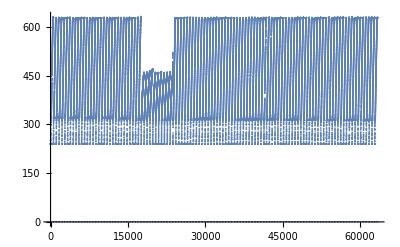

```mathematica
ListPlot[data[[All,12]]]
```

```mathematica
values={"ID", "Time", "TAmbient", "Ttc", "Vb", "dV", "P1", "P2", "TInlet", "TOutlet", "Detector", "TColumn", "Vcol","P1 Setpoint", "P2 Setpoint", "TInlet Setpoint", "TOutlet Setpoint", "TColumn Setpoint"}
```

{ID,Time,TAmbient,Ttc,Vb,dV,P1,P2,TInlet,TOutlet,Detector,TColumn,Vcol,P1 Setpoint,P2 Setpoint,TInlet Setpoint,TOutlet Setpoint,TColumn Setpoint}

```mathematica
Join[{values}, {Range[18] } ]//TableForm
```

ID | Time | TAmbient | Ttc | Vb | dV | P1 | P2 | TInlet | TOutlet | Detector | TColumn | Vcol | P1 Setpoint | P2 Setpoint | TInlet Setpoint | TOutlet Setpoint | TColumn Setpoint
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18

Split the data by ID. Turns the list into a list of lists.

```mathematica
data2 = Split[data, #1[[1]]==#2[[1]]&];
```

```mathematica
Length[data]
```

63370

```mathematica
Length[data2]
```

344

Find the times of the GC runs. This counts the number of GC runs, i.e. the length of the first dimension.

```mathematica
d1 = Select[data, #[[1]]==1&][[All, 2]];
```

```mathematica
d1
```

{479.9,481.9,483.9,486.,488.,490.,492.,494.,496.,498.,500.,502.,504.,506.,508.,510.,512.,514.,516.,518.,520.,522.,524.,526.,528.,530.,532.,534.,536.,538.1,540.1,542.1,544.1,546.1,548.1,550.1,552.1,554.1,556.1,558.1,560.1,562.2,564.2,566.2,568.2,570.2,572.2,574.2,576.2,578.2,580.2,582.2,584.2,586.2,588.2,590.2,592.2,594.2,596.2,598.2,600.2,602.2,604.2,606.2,608.2,610.2,612.2,614.2,616.2,618.2,620.2,622.2,624.3,626.3,628.3,630.3,632.3,634.3,636.3,638.3,640.3,642.3,644.3,646.3,648.3,650.3,652.3,654.3,656.3,658.3,665.3,672.3,679.3,686.3,693.4,700.4,705.4,707.4,712.4,717.4,722.4,729.4,736.4,743.,749.,755.,757.,759.,761.,762.9,766.9,770.9,774.9,778.9}

The number of GC runs:

```mathematica
Length[d1]
```

114

Check data integrity:
Number of GC runs (ID=2) + 2 per GC run (ID=1 and ID = 3) + ID=0 and ID=4

```mathematica
Length[d1]+Length[d1]*2 + 2
```

344

Plot a GC run to see if looks sane:

```mathematica
Manipulate[
ListLinePlot[
	Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
	, PlotLabel ->values[[dataset]]
]
	,{{gcrun,1,"GC Run"},1, Length[d1],1}
	,{{dataset,11, "Dataset"},1,18,1}
]
```

```mathematica
.
```

Delete wrong data:

First identify index of wrong data

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[107]][[All,2]]
```

{0.033,0.056,0.079,0.114,0.137,0.159,0.182,0.207,0.23,0.252,0.274,0.297,0.319,0.341,0.365,0.387,0.409,0.448,0.471,0.494,0.516,0.538,0.561,0.583,0.622,0.645,0.667,0.69,0.714,0.737,0.759,0.782,0.821,0.845,0.867,0.889,0.923,0.946,0.968,0.991,1.032,1.054,1.078,1.118,1.141,1.163,1.186,1.215,1.238,1.261,1.283,1.317,1.34,1.363,1.385,1.407,1.441,1.463,1.485,1.525,1.548,1.571,1.593,1.616,1.638,1.661,1.683,1.705,1.745,1.767,1.789,1.819,1.842,1.864,1.888,1.91,1.932,1.955,1.977,1.999,2.025,2.047,2.069,2.091,2.113,2.136,2.158,2.18,2.202,2.242,2.265,2.287,2.309,2.332,2.355,2.377,2.399,2.422,2.444,2.466,2.488,2.511,2.534,2.557,2.579,2.619,2.641,2.664,2.686,2.718,2.74,2.763,2.785,2.809,2.831,2.854,2.875,2.898,2.92,2.942,2.964,2.987,3.009,3.032,3.055,3.078,3.119,3.142,3.165,3.187,3.215,3.24,3.263,3.285,3.323,3.349,3.371,3.393,3.432,3.455,3.478,3.5,3.534,3.556,3.578,3.618,3.64,3.663,3.686,3.711,3.734,3.757,3.779,3.817,3.84,3.863,3.885,3.913,3.936,3.958,3.981,4.017,4.04,4.063,4.085,4.117,4.14,4.162,4.184,4.21,4.234,4.257,4.279,4.301,4.341,4.364,4.386,4.411,4.439,4.461,4.483,4.515,4.538,4.56,4.583,4.613,4.636,4.658,4.68,4.712,4.734,4.757,4.779,4.813,4.836,4.86,4.882,4.911,4.933,4.955,4.978,5.,5.035,5.058,5.08,5.106,5.128,5.152,5.174,5.197,5.219,5.241,5.264,5.286,5.311,5.335,5.359,5.381,5.403,5.44,5.464,5.486,5.514,5.537,5.561,5.583,5.609,5.632,5.655,5.677,5.699,5.722,5.746,5.768,5.79,5.82,5.845,5.868,5.89,5.914,5.937,5.961,5.983,6.01,6.032,6.054,6.077,6.099,6.122,6.145,6.167,6.189,6.211,6.233,6.256,6.278,6.313,6.337,6.36,6.382,6.419,6.441,6.465,6.487,6.51,6.533,6.556,6.578,6.611,6.633,6.655,6.677,6.7,6.722,6.744,6.767,6.79,6.814,6.838,6.86,6.883,6.907,6.93,6.954,6.977,6.999,7.021,7.045,7.07,7.093,7.115,7.139,7.162,7.184,7.209,7.231,7.253,7.276,7.298,7.32,7.343,7.366,7.388,7.411,7.433,7.457,7.479,7.513,7.536,7.56,7.582,7.608,7.632,7.655,7.677,7.699,7.721,7.745,7.767,7.789,7.813,7.836,7.859,7.882,7.908,7.931,7.954,7.977,7.999,8.022,8.044,8.066,8.088,8.111,8.133,8.155,8.177,8.2,8.234,8.257,8.279,8.306,8.33,8.352,8.375,8.397,8.419,8.442,8.464,8.487,8.511,8.534,8.557,8.579,8.605,8.628,8.651,8.673,8.696,8.718,8.741,8.765,8.787,8.81,8.833,8.855,8.877,8.913,8.935,8.959,8.981,9.007,9.03,9.052,9.077,9.099,9.122,9.144,9.166,9.191,9.221,9.244,9.266,9.289,9.311,9.333,9.358,9.38,9.411,9.434,9.457,9.479,9.509,9.531,9.555,9.577,9.599,9.622,9.646,9.668,9.69,9.713,9.736,9.759,9.781,9.814,9.837,9.859,9.882,9.908,9.93,9.954,9.976,9.998,10.021,10.043,10.066,10.088,10.114,10.137,10.16,10.183,10.21,10.233,10.256,10.278,10.313,10.337,10.359,10.381,10.409,10.432,10.453,10.476,10.498,10.52,10.543,10.565,10.587,10.61,10.632,10.656,10.678,10.7,10.736,10.76,10.782,10.814,10.836,10.858,10.881,10.908,10.93,10.955,10.977,10.999,11.022,11.044,11.066,11.089,11.111,11.133,11.155,11.178,11.2,11.222,11.244,11.267,11.289,11.312,11.334,11.358,11.381,11.413,11.436,11.46,11.482,11.512,11.535,11.558,11.581,11.606,11.629,11.652,11.675,11.697,11.727,11.75,11.774,11.824,11.846,11.869,11.891,11.925,11.948,11.971,11.993,12.016,12.038,12.062,12.086,12.116,12.139,12.161,12.183,12.217,12.241,12.264,12.286,12.309,12.332,12.354,12.377,12.4,12.422,12.446,12.468,12.491,12.513,12.536,12.558,12.58,12.617,12.64,12.664,12.686,12.709,12.731,12.755,12.777,12.799,12.822,12.845,12.867,12.89,12.921,12.944,12.966,12.989}

Delete wrong data:

```mathematica
data2[[107*3+1+2]]=0
```

0

Check that data was deleted

```mathematica
data2[[109*3+1+2]][[-12;;-1]]
```

{{2,12.543,304.292,339.084,5.62898,6.11005,2.03211×10^7,-818256.,623.975,631.091,0.051535,629.374,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.565,304.293,339.085,5.62948,6.1097,2.03214×10^7,-818565.,624.021,631.109,0.0514587,629.225,-0.012323,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.588,304.294,339.097,5.62956,6.11065,2.03207×10^7,-817978.,624.073,631.129,0.0513306,629.371,-0.0124054,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.61,304.293,339.077,5.63014,6.10977,2.03209×10^7,-817792.,624.078,631.125,0.0511719,629.117,-0.0124908,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.636,304.292,339.096,5.5837,6.05612,2.03232×10^7,-815319.,624.035,631.075,0.051297,628.567,-0.0121246,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.658,304.291,339.077,5.55763,6.03091,2.03235×10^7,-816463.,624.128,631.165,0.0512878,629.088,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.681,304.291,339.077,5.55432,6.02879,2.03216×10^7,-816958.,624.1,631.165,0.0511505,629.339,-0.0126221,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.713,304.295,339.077,5.55583,6.0275,2.03211×10^7,-815350.,624.128,631.153,0.0510529,628.84,-0.012735,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.735,304.293,339.101,5.53895,6.01089,2.0324×10^7,-815195.,624.152,631.109,0.0510132,629.129,-0.0126862,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.758,304.293,339.094,5.53032,6.00199,2.03235×10^7,-815597.,624.228,631.211,0.0510376,629.21,-0.0126617,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.78,304.293,339.102,5.52975,6.00178,2.03237×10^7,-815319.,624.24,631.227,0.0511139,629.28,-0.0128387,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.81,304.292,339.11,5.53023,6.00126,2.03217×10^7,-815350.,624.219,631.232,0.0510315,629.102,-0.0127441,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15}}

```mathematica
Drop[data2, {42*3+1+2,
```

Examine data in relation with temperature:

```mathematica
Manipulate[
ListLinePlot[
Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
, PlotLabel ->values[[dataset]]
,PlotRange->Automatic
,AxesLabel->{"Time (s)"}
, Epilog->{Scale[
Point[
Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,12}]]
]
,{1,1./70.}
,{0,0}
]
}
](* Ends ListLine Plot*)
,{{gcrun,1,"GC Run"},1, Length[d1],1}
,{{dataset,11, "Dataset"},1,18,1}
] (* Ends Manipulate *)
```

Print an SFC time to see if it looks sane

```mathematica
d1[[1]]
```

479.9

Create 3D values {t_r1,t_r2,det}

```mathematica
Clear[f]
```

```mathematica
f[x_, y_]:= {Map[Prepend[#,x]&,y]}
```

The number of GC runs:

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]]//Length
```

114

```mathematica
Length[d1]
```

114

```mathematica
data2d =Inner[f, d1, Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]], Join];
```

```mathematica
params //TableForm
```

GC column description:	Rxi-5Sil MS 0.250 mm x 1 m
SFC flow rate:	0.800
SFC temperature:	22.000
GC flow rate: 	99.000
Experiment title: 	Diesel PAH
Sample name: 	US 2D Reference Fuel
Analysis type: 	Standard
Concentration: 	9999.000
Operator name: 	DM
Detector sensitivity: 	1.0E-9
FID H2 flow rate: 	36.700
FID Air flow rate: 	300.000
SFC pressure: 	20265000 Pa
SFC dead time: 	480.000 s
File name: 	C:\SFC-GC\Data\2020_01_20-123917.dat
SFC gradient0:
Rate: 	0 $1 s^-1
Final:	0.000000 $1
Time:	2700.000 s
GC gradient0:
Rate: 	0 $1 s^-1
Final:	253.150000 $1
Time:	0.000 s
GC gradient1:
Rate: 	133 $1 s^-1
Final:	298.150000 $1
Time:	0.000 s
GC gradient2:
Rate: 	33 $1 s^-1
Final:	623.150000 $1
Time:	2.000 s
GC idle temperature:	323.100000 Cdeg
GC purge temperature: 	473.150000 Cdeg
GC sampling temperature: 	239.850000 Cdeg
GC sampling time: 	2
GC load time: 	3
GC vent time: 	1

```mathematica
plot3d = ListPlot3D[
Flatten[data2d,1]
,PlotRange->{All, All, All}
,AxesLabel->{"SFC (s)", "GC (s)","Detector (V)"}
,PlotLabel->StringSplit[params[[6]], ":"][[2]]
,Mesh -> None

(*, ColorFunction->"BlueGreenYellow"*)
]
```

-Graphics3D-

```mathematica
Show[plot3d, PlotRange->{All,All,{-0.5,10}}]
```

-Graphics3D-

```mathematica
Show[plot3d, PlotRange->{{1400,2400},All,{-0.5,10}}]
```

-Graphics3D-

```mathematica
Show[plot3d, PlotRange->{{400,1000},All,All}]
```

-Graphics3D-

```mathematica
Show[plot3d, Graphics3D[{Red,Line[data2d]}], PlotRange->{{400,800},All,All}]
```

-Graphics3D-

Make a virtual SFC Chromatogram:

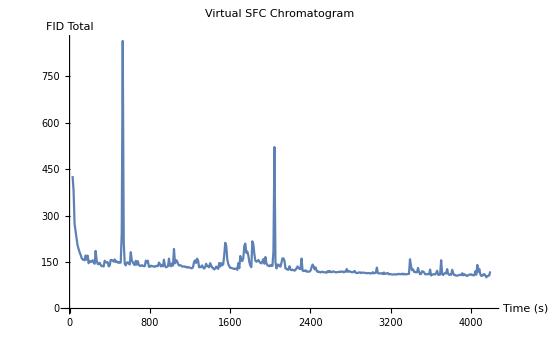

```mathematica
ListLinePlot[Partition[Riffle[d1,(Total[#]&/@data2d)[[All,3]]],2], PlotLabel->"Virtual SFC Chromatogram", AxesLabel->{"Time (s)","FID Total"}, PlotRange->All]
```

Create graphics for export to the thesis or publication:

```mathematica
exportgraphic = Show[
	plot3d
	,PlotLabel -> Style["FAMEs: Canola oil", Large, Bold, Black]
	, AxesStyle -> {Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				}
	,AxesLabel-> 
		{Style["SFC (s)", Large, Bold, Black]
		, Style[ "GC (s)",Large, Bold, Black]
		,Style[Rotate["Detector (V)", 90 Degree], Large, Bold, Black]
		}
	(*, ViewPoint->{10000,10000,10000} *)
	, ImageSize-> 1024
	, ViewPoint->vp
	
]
```

-Graphics3D-

```mathematica
Export["C:\\Users\\fskdm\\My PhD\\Conferences\\Analitika 2018\\Poster\\images\\Canola.png",exportgraphic,Background->None, ViewPoint->vp]
```

C:\Users\fskdm\My PhD\Conferences\Analitika 2018\Poster\images\Canola.png

```mathematica
Show[
	plot3d
(*	,Graphics3D[{Red,Line[data2d]}] *)
     , PlotLabel -> "Mystery Oil"
	, PlotRange-> {All, All,{0,0.1}}
]
```

```mathematica
ListContourPlot[Flatten[data2d,1], PlotRange->{All, All, All}, AxesLabel->{"SFC (s)", "GC (s)"}]
```

-Graphics-

ListLinePlot::lpn: {{{2.,0.031,303.909,293.693,1.64702,0.9578,2.02274×10^7,158135.,586.294,593.745,4.80018,239.804,4.38922,2.0265×10^7,2.76769×10^7,623.15,623.15,253.15},{2.,0.053,303.909,293.68,1.65988,0.962924,2.02255×10^7,160268.,586.189,593.742,4.80303,239.804,4.39384,2.0265×10^7,2.76769×10^7,623.15,623.15,253.15},«48»,«530»},{«1»},«48»,«322»}⟦417⟧⟦All,{2,9}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Part::partd: Part specification {{{2,0.032,301.42,293.411,0.697638,0.425607,2.02435×10^7,158320.,593.005,617.12,9.99969,249.05,9.99969,2.0265×10^7,2.76769×10^7,673.15,653.15,253.15},{2,0.054,301.42,293.387,0.784052,0.466101,2.02426×10^7,157485.,592.853,616.986,9.99969,239.804,9.99969,2.0265×10^7,2.76769×10^7,673.15,653.15,253.15},«48»,«493»},{«1»},{«1»},«46»,{{2,«16»,253.15},«49»,«518»},«64»}⟦382⟧⟦«1»⟧ is longer than depth of object.

Part::partw: Part 382 of {{{2.,0.032,301.42,293.411,0.697638,0.425607,2.02435×10^7,158320.,593.005,617.12,9.99969,249.05,9.99969,2.0265×10^7,2.76769×10^7,673.15,653.15,253.15},{2.,0.054,301.42,293.387,0.784052,0.466101,2.02426×10^7,157485.,592.853,616.986,9.99969,239.804,9.99969,2.0265×10^7,2.76769×10^7,673.15,653.15,253.15},«48»,«493»},{{2.,«16»,253.15},«49»,«498»},«47»,{«1»},«64»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification {{{2.,0.032,301.42,293.411,0.697638,0.425607,2.02435×10^7,158320.,593.005,617.12,9.99969,249.05,9.99969,2.0265×10^7,2.76769×10^7,673.15,653.15,253.15},{2.,0.054,301.42,293.387,0.784052,0.466101,2.02426×10^7,157485.,592.853,616.986,9.99969,239.804,9.99969,2.0265×10^7,2.76769×10^7,673.15,653.15,253.15},«48»,«493»},«49»,«64»}⟦382⟧⟦All,{2,11}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted[]

ListLinePlot::lpn: {{{2.,0.032,301.42,293.411,0.697638,0.425607,2.02435×10^7,158320.,593.005,617.12,9.99969,249.05,9.99969,2.0265×10^7,2.76769×10^7,673.15,653.15,253.15},{2.,0.054,301.42,293.387,0.784052,0.466101,2.02426×10^7,157485.,592.853,616.986,9.99969,239.804,9.99969,2.0265×10^7,2.76769×10^7,673.15,653.15,253.15},«48»,«493»},{{2.,«16»,253.15},{«1»},«48»,«498»},«48»,«64»}⟦382⟧⟦«1»⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.